# Stability analyses under accelerating returns

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]];
```

## 1. Functions

```mathematica
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
Functions = { Bc->Function[k,n (k/n)^u β]};
```

```mathematica
values={n->4,β->1,Cc-> 0.3,δ->1,u->2,cd-> 0.5} ;

cm=72/2.54;
```

```mathematica
graphicspPayoffs=ListPlot[Table[{k,(k/n)^u β  }/.values,{k,0,4}],Filling->Axis,PlotStyle->Gray,Frame->True,FrameTicks->{{{0,0.5,1},None},{{0,1,2,3,4},None}},ImageSize->8cm,FrameLabel->{k,Rotate[Subscript[B, k]/N,-Pi/2]},LabelStyle->Directive[FontFamily->"Arial",FontSize->17,Black],PlotMarkers->{Automatic,15},PlotRange-> {{-0.2,4.2},{-0.1,1.1}}]
```

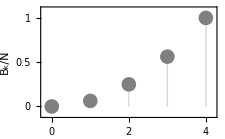

Figure 3a of the main text

```mathematica
Export["Payoff_Acc.pdf",Show[graphicspPayoffs,ImageSize->8 cm]]
```

Payoff_Linear.pdf

## 2. Numerical analyses

Here we perform numerical stability analyses,looking for a value of x=(z,d_0,...,d_N) where directional selection is null on all traits. We also compute the singular value under unconditional dispersal(when d_0=d_1=...=d_N) To do so, we use the Mathematica function "FindRoot". This corresponds to the procedure described in section 3.3 of the main text and section D.3.1 of the Appendix. We also compute whether the singular strategy found is convergence stable by computing the eigenvalues if the Jacobian Matrix at the singular strategy (procedure described in Appendix D.3.2. We write the results obtained in a .txt file.

```mathematica
(************************** Parameters to be used ************************)
rangeu=Subdivide[1.5,2.5,2];
rangecd=Subdivide[0.05,0.95,18];
values={n->4,β->1.,Cc-> 0.3,δ->1.} ;
nval= n /. values;
βval=β/.values;
Ccval=Cc/.values;
δval=δ/.values;
valuesNeutral={n->nval,δ->0} ;

Functions = { Bc->Function[k,n(k/n)^u β]};

(****** Define the important functions *******)
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)); (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
fecloc=( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) );
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)
m[k0_]:=fecdisp[d[n+1]] /(fecphilo[k0]+fecdisp[d[n+1]] )/.valuesNeutral;

monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,nval+1},{i,1,3}]];
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,nval},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,nval} ]];
w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(fecloc+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.Functions/.values;
(* Fitness of a focal individual*)

wP1=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 (fec[c1+c2+c3+c0,c1](  1-d[1,c1+c2+c3+c0])/(fecloc+ fecdisp[d[n+1]]))^2 d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.Functions/.values;
(* Average philopatric fitness, squared*)

R2 == ∑_(k0 =0)^n (1-m[k0])^2(1/n+((n-1)/n)R2)Pk0[k0,d[n+1],n]/.valuesNeutral;
solR2=Flatten[Solve[%,R2]];
solR2R={R2R->1/n+((n-1)/n)R2/.solR2};
R3 == ∑_(k0=0)^n (1-m[k0])^3(1/n^2+ 3((n-1)/n^2)R2+(((n-1)(n-2))/n^2)R3) Pk0[k0,d[n+1],n]/.valuesNeutral;
solR3=Flatten[Solve[%,R3]];
ΔR2dUncondi[x_]:=
R2R((1+(n-1)R2)D[wP1/.uncond1/.uncond2, d[1,x]] +(n-1)(2R2+(n-2)R3)D[wP1/.uncond1/.uncond2, d[2,x]])/. monopop /.solR2R/.solR3/. solR2  /.values
ΔR2d [x_]:=
R2R((1+(n-1)R2)D[wP1, d[1,x]] +(n-1)(2R2+(n-2)R3)D[wP1, d[2,x]])/. monopop /.solR2R/.solR3/. solR2  /.values
SUncondi=
Table[
D[w/.uncond1 /.uncond2, d[1,k]]+ (n-1)R2 D[w/.uncond1/.uncond2, d[2,k]]/. solR2 /. monopop /.uncond2/.values
,{k,{0,nval+1}}];
HUncondi=Table[D[w/.uncond1/.uncond2, d[1,x1],d[1,x2]]  + R2(n-1)   D[w/.uncond1/.uncond2, d[2,x1],d[2,x2]] +R2(n-1)   ( D[w/.uncond1/.uncond2, d[1,x1],d[2,x2]] + D[w/.uncond1/.uncond2,d[2,x1],d[1,x2]] ) + R3 (n-1)(n-2)  D[w/.uncond1/.uncond2,d[2,x1],d[3,x2]]+(n-1)D[w/.uncond1/.uncond2,d[2,x1]]ΔR2dUncondi[x2]+(n-1)D[w/.uncond1/.uncond2,d[2,x2]]ΔR2dUncondi[x1] /.monopop/.solR2R /.solR3/. solR2  /.values,{x1,{0,nval+1}},{x2,{0,nval+1}}]/. monopop /.uncond2/.values;

SCondi=Table[
D[w, d[1,x]]+ (n-1)R2 D[w, d[2,x]]/. solR2 /. monopop /.values
,{x,0,nval+1}];
HCondi=Table[D[w, d[1,x1],d[1,x2]]  + R2(n-1)   D[w, d[2,x1],d[2,x2]] +R2(n-1)   ( D[w, d[1,x1],d[2,x2]] + D[w,d[2,x1],d[1,x2]] ) + R3 (n-1)(n-2)  D[w,d[2,x1],d[3,x2]]+(n-1)D[w,d[2,x1]]ΔR2d[x2]+(n-1)D[w,d[2,x2]]ΔR2d[x1] /.monopop/.solR2R /.solR3/. solR2  /.values,{x1,0,nval+1},{x2,0,nval+1}];

(****** Creating the results file *******)
f="Accelerating_B_"<>TextString[βval]<>"_C_"<>TextString[Ccval]<>"_d_"<>TextString[δval]<>"_n_"<>TextString[nval]<>".txt"/.values;
If[!FileExistsQ[f], (* If it does not exist yet, create it and include a header with the name of columns *)
CreateFile[f];
Close[f] //Quiet;
stream=OpenAppend[f];
WriteLine[stream,"cd u dU zU J H d(n+1) z J H ds"];
];
Close[f] //Quiet;

stream=OpenAppend[f]; (* Output stream *)
Table[
cc=0;
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values/.cd->cdtab;
SUncondiTab=Evaluate[SUncondi/.cd->cdtab/.u->utab];
equiUncondi=FindRoot[Table[SUncondiTab[[i]]==0,{i,1,2}], {d[0],d0baseline,0,1},{d[nval+1],If[cdtab==0.05,0.75,startz0 ]  }] ;
startz0 = Last[equiUncondi][[2]];
d0 = First[equiUncondi][[2]];

SCondiTab=Evaluate[SCondi/.cd->cdtab/.u->utab];
equiCondi=FindRoot[Table[SCondiTab[[i]]==0,{i,1,nval+2}], Append[ Table[ {d[k],d0baseline},{k,0,nval}] ,{d[nval+1], If[cdtab==0.05,startz0,startz ]  }]] ;
startz = Last[equiCondi][[2]];

JTabUncondi=D[SUncondiTab,{Table[ d[k],{k,{0,nval+1}}]}]/.equiUncondi;
JmaxUncondi=Re[Eigenvalues[JTabUncondi]]//Max;
HTabUncondi=HUncondi/.equiUncondi/.cd->cdtab/.u->utab;
HmaxUncondi=Eigenvalues[HTabUncondi]//Max;
If[JmaxUncondi<0,Print["stable equilibrium"];cc=1];
JTabCondi=D[SCondiTab,{Table[ d[k],{k,0,nval+1}]}]/.equiCondi;
JmaxCondi=Re[Eigenvalues[JTabCondi]]//Max;
If[JmaxCondi<0,Print["stable equilibrium"];cc=1];
HTabCondi=HCondi/.equiCondi/.cd->cdtab/.u->utab;
HmaxCondi=Eigenvalues[HTabCondi]//Max;
res=Flatten[{cdtab, utab,d0,startz0,JmaxUncondi,HmaxUncondi,Table[d[k]/.equiCondi,{k,0,nval} ] ,startz,JmaxCondi,HmaxCondi,Total[Chop@(SCondiTab/.equiCondi) ]}/.equiCondi];
str=StringRiffle[res];
WriteLine[stream,str];
,{utab,rangeu},{cdtab,rangecd}]
If[cc==0,Print["all equilibrium found are unstable"]]
```

$Aborted

$Aborted

$Aborted

all equilibrium found are unstable

## Read the analyses (Fig 5c, Fig S2a-c)

In this section we read the  . txt file obtained from the previous section and draw fig 5c of the main text and Fig S2a-c of the appendix.

```mathematica
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
cm=72/2.54;
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
rImport[βval_,Ccval_,δval_,nval_]:=Import["Accelerating_B_"<>TextString[βval]<>"_C_"<>TextString[Ccval]<>"_d_"<>TextString[δval]<>"_n_"<>TextString[nval]<>".txt","Table"];
ztrait[βval_,Ccval_,δval_,nval_,cdvect_,uval_]:=(
results=rImport[βval,Ccval,δval,nval];
results=Delete[results,1];
Listres=Select[results,#[[2]]==uval&];
traits=Table[a=Select[Listres,#[[1]]==cdi&];a,{cdi,cdvect}];
traits=Transpose[Flatten[traits,1]][[{1,4,-4}]]
);
```

```mathematica
cdv=Subdivide[0.05,0.95,18]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

```mathematica
PlotHelp[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
x0=ztrait[βval,Ccval,δval,nval,cdvect,uval];
p1=ListPlot[ Transpose[{cdvect,x0[[2]]}],PlotMarkers->Style[shape,size],PlotStyle->Gray];
p2=ListPlot[  Transpose[{cdvect,x0[[3]]}],PlotMarkers->Style[shape,size],PlotStyle->orange];
Show[p2,p1,LabelStyle->Directive[FontFamily->" Arial",FontSize->12,Black],FrameTicks->{{{0,0.25,.5,0.75},None},{{0,.5,1},None}},Frame->True,PlotRange->{{0,1},{-0.01,0.85}},AspectRatio->0.85,FrameLabel->{None,"z^*"},RotateLabel->False])
```

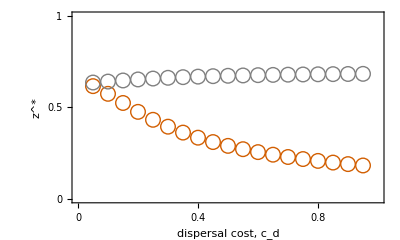

Acc_main.pdf

```mathematica
p2=Show[PlotHelp[1.,0.3,1.,4,cdv,2,○,15],AspectRatio->0.6,PlotRangePadding->0,FrameTicks->{{{0,.5,1},None},{{0,.2,.4,.6,.8,1},None}},PlotRange->{{0,1},{0,1}},FrameLabel->{"dispersal cost, c_d","z^*"},LabelStyle->Directive[FontFamily->"Arial",FontSize->16,Black]]
Export["Acc_main.pdf",p2,ImageSize->11cm]
```

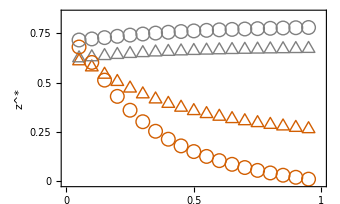

```mathematica
p25=PlotHelp[1.,0.3,1.,4,cdv,1.5,○,14];
p15=PlotHelp[1.,0.3,1.,4,cdv,2.5,△,15];
plot=Show[p15,p25,AspectRatio->0.6,ImageSize->12cm]
```

```mathematica
Export["Acc_u.pdf",plot,ImageSize->12cm]
```

Acc_u.pdf

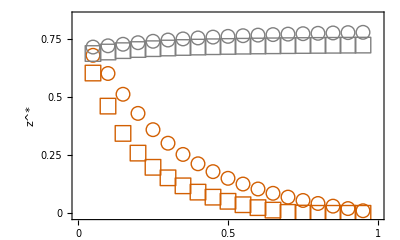

```mathematica
p6=PlotHelp[1.5,0.3,1.,6,cdv,1.5,□,16];
p4=PlotHelp[1.0,0.3,1.,4,cdv,1.5,○,14];
plot=Show[p4,p6,AspectRatio->0.6]
```

```mathematica
Export["Acc_N.pdf",plot,ImageSize->12cm]
```

Acc_N.pdf

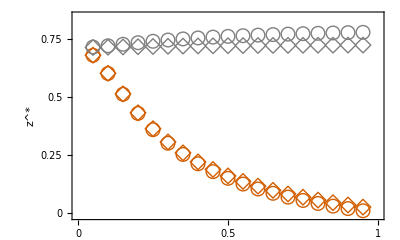

```mathematica
p1d=PlotHelp[1.0,0.3,.1,4,cdv,1.5,◇,16];
p15=PlotHelp[1.0,0.3,1.,4,cdv,1.5,○,14];
plot=Show[p15,p1d,AspectRatio->0.6]
```

```mathematica
Export["Acc_delta.pdf",plot,ImageSize->12cm]
```

Acc_delta.pdf